```mathematica
Needs["OpenCLLink`"]
```

```mathematica
mas=Import[NotebookDirectory[]<>"hexaflake_0.800000_2.txt","Table"];
data=mas[[2;;All]];
(*data=Map[Partition[#,2]&,data];
datap=Map[{Red,Polygon[#]}&,data];
Graphics[datap]*)
```

```mathematica
{countpoly,pointsperpoly}=Dimensions[data]
```

{128,204}

```mathematica
fdata=Flatten[data];
size=Length[fdata];
```

```mathematica
src=Import[NotebookDirectory[]<>"HexFlakeOCLKernel.c","Text"];
```

```mathematica
fun=OpenCLFunctionLoad[src,"Step",{{"Float","Output"},{"Float","Output"},{"Float","Output"},{"Float","Output"},{"Integer32","Output"},{"Integer32","Input"}},32,"ShellOutputFunction"->Print ];
```

```mathematica
initdata=mas[[1]];
```

```mathematica
lattice=Table[fdata[[i]],{i,size}];
probelattice=Table[0.0,{i,size}];
centers=Flatten[Table[{Mean[data[[i]][[1;;All;;2]]],Mean[data[[i]][[2;;All;;2]]]},{i,countpoly}]];
params={size,countpoly,initdata[[3]],initdata[[4]],initdata[[5]],initdata[[6]]};
accept=Table[0,{i,countpoly}];
seed=RandomInteger[{100000000,1000000000},countpoly];
```

```mathematica
res=fun[lattice,probelattice,centers,params,accept,seed];//Timing
```

```mathematica
resp=Partition[res[[1]], pointsperpoly];
data1=Map[Partition[#,2]&,resp];
datap=Map[{Red,Polygon[#]}&,data1];
Graphics[datap]
```

```mathematica
gdata=Map[Partition[#,2]&,Import[NotebookDirectory[]<>"hexaflake_0.800000_0.txt","Table"][[2;;All]]];
datap=Map[{EdgeForm[Thick],Red,Polygon[#]}&,gdata];
```

```mathematica
xc=gdata[[1]][[1;;All,1]]//Mean;
yc=gdata[[1]][[1;;All,2]]//Mean;
```

```mathematica
gdata[[1]][[All,1]]=gdata[[1]][[All,1]]-xc;
gdata[[1]][[All,2]]=gdata[[1]][[All,2]]-yc;
```

```mathematica
gdata0=MapThread[{#1,#2}/0.8&,{gdata[[1]][[All,1]],gdata[[1]][[All,2]]}];
```

```mathematica
gdata0[[1;;All;;1]]
```

{{3.46945×10^-17,0.857143},{-0.866025,0.357143},{-0.866025,-0.642857},{3.46945×10^-17,-1.14286},{0.866025,-0.642857},{0.866025,0.357143},{3.46945×10^-17,0.857143}}

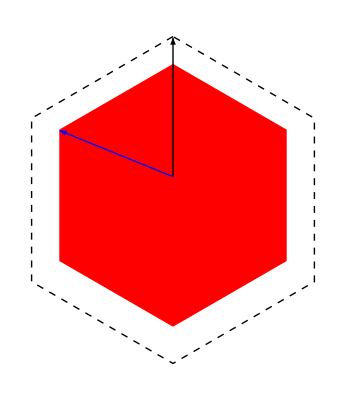

```mathematica
Graphics[{{EdgeForm[Thick],Red,Polygon[gdata[[1]]]},{Thick,Arrow[{{0,0},{0,0.85}}]},{Thick,Blue,Arrow[{{0,0},RotationMatrix[Pi/2.65].{0,0.75}}]},{Dashed,Line[gdata0[[1;;All;;1]]]}}]
```

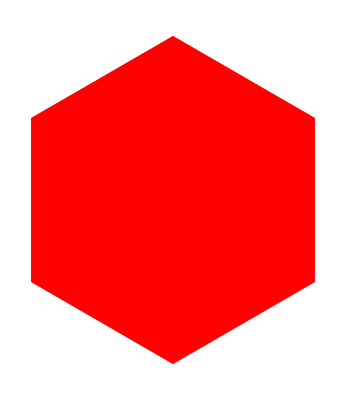

```mathematica
Graphics[{{EdgeForm[Thick],Red,Polygon[gdata[[1]]]}}]
```

```mathematica
xc
```

0.2

```mathematica
yc
```

0.814286

```mathematica
gdata[[1]]
```

{{0.,0.752941},{0.,0.752941},{0.,0.752941},{0.,0.752941},{0.,0.752941},{0.,0.752941},{-0.07698,0.708496},{-0.07698,0.619608},{-0.15396,0.664052},{-0.23094,0.619608},{-0.23094,0.530719},{-0.15396,0.486274},{-0.23094,0.44183},{-0.23094,0.352941},{-0.30792,0.397385},{-0.3849,0.352941},{-0.3849,0.44183},{-0.46188,0.486274},{-0.53886,0.44183},{-0.53886,0.352941},{-0.61584,0.397385},{-0.69282,0.352941},{-0.69282,0.264052},{-0.61584,0.219608},{-0.69282,0.175163},{-0.69282,0.0862743},{-0.61584,0.0418303},{-0.53886,0.0862743},{-0.53886,-0.00261475},{-0.46188,-0.0470587},{-0.53886,-0.0915037},{-0.53886,-0.180392},{-0.61584,-0.135948},{-0.69282,-0.180392},{-0.69282,-0.269281},{-0.61584,-0.313726},{-0.69282,-0.35817},{-0.69282,-0.447059},{-0.61584,-0.491504},{-0.53886,-0.447059},{-0.53886,-0.535948},{-0.46188,-0.580392},{-0.3849,-0.535948},{-0.3849,-0.447059},{-0.30792,-0.491504},{-0.23094,-0.447059},{-0.23094,-0.535948},{-0.15396,-0.580392},{-0.23094,-0.624837},{-0.23094,-0.713726},{-0.15396,-0.75817},{-0.07698,-0.713726},{-0.07698,-0.802615},{0.,-0.847059},{0.07698,-0.802615},{0.07698,-0.713726},{0.15396,-0.75817},{0.23094,-0.713726},{0.23094,-0.624837},{0.15396,-0.580392},{0.23094,-0.535948},{0.23094,-0.447059},{0.30792,-0.491504},{0.3849,-0.447059},{0.3849,-0.535948},{0.46188,-0.580392},{0.53886,-0.535948},{0.53886,-0.447059},{0.61584,-0.491504},{0.69282,-0.447059},{0.69282,-0.35817},{0.61584,-0.313726},{0.69282,-0.269281},{0.69282,-0.180392},{0.61584,-0.135948},{0.53886,-0.180392},{0.53886,-0.0915037},{0.46188,-0.0470587},{0.53886,-0.00261475},{0.53886,0.0862743},{0.61584,0.0418303},{0.69282,0.0862743},{0.69282,0.175163},{0.61584,0.219608},{0.69282,0.264052},{0.69282,0.352941},{0.61584,0.397385},{0.53886,0.352941},{0.53886,0.44183},{0.46188,0.486274},{0.3849,0.44183},{0.3849,0.352941},{0.30792,0.397385},{0.23094,0.352941},{0.23094,0.44183},{0.15396,0.486274},{0.23094,0.530719},{0.23094,0.619608},{0.15396,0.664052},{0.07698,0.619608},{0.07698,0.708496},{0.,0.752941}}

```mathematica
2*128^2
```

512/3

```mathematica
Divisors[32768]
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768}

```mathematica
64*3
```

192

```mathematica
128*130+(3200-128)*3
```

25856

```mathematica
r=0.9;
6*r^2*Sin[30 Degree]*Cos[30 Degree]/(Pi*Cos[30 Degree]^2)
```

0.893153

```mathematica
0.81*0.906900
```

0.734589

```mathematica
Sqrt[0.71]
```

0.842615